```mathematica
ClearAll["Global`*"]
(*
	The orbital projection measure Subscript[μ, λ]:
	Subscript[μ, λ]^p = ∑_(w∈W) sgn(w) Subscript[e, wλ] * P,    P_= ∏_(α∈Φ^+) * Subscript[F, α]

My appoarch is:

  Subscript[μ, λ]^p = lim_(n -> ∞) ∑_(w∈W) sgn(w) Subscript[e, wλ] * Subscript[P, n]       where Subscript[P, n]= ∏_(α∈Φ^+) *Subscript[F, nα]
*)
```

```mathematica
(* Definie the basic infomation including root system of Subscript[A, 2] *)
Subscript[α, 1]={√2,0}; T={{Cos[2π/3],-Sin[2π/3]},{Sin[2π/3],Cos[2π/3]}};  
δ=Subscript[α, 1]+T.Subscript[α, 1]; λ1=(1/3)*(2 Subscript[α, 1]+T.Subscript[α, 1]); λ2=(1/3)*(Subscript[α, 1]+2T.Subscript[α, 1]);   a1= Subscript[α, 1];  a2=T.Subscript[α, 1];
origin = {0,0};
roots = {δ,-δ,Subscript[α, 1],-Subscript[α, 1],T.Subscript[α, 1],-T.Subscript[α, 1]};
```

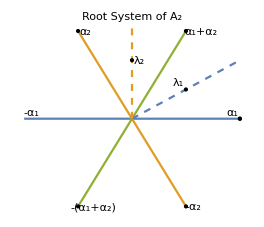

```mathematica
(* Plot the Root System of Subscript[A, 2] *)
p1=ListLinePlot[{{-Subscript[α, 1], Subscript[α, 1]},{-T.Subscript[α, 1], T.Subscript[α, 1]},{-(Subscript[α, 1]+T.Subscript[α, 1]), Subscript[α, 1]+T.Subscript[α, 1]}},AspectRatio->Automatic,Axes->False,PlotLabel->Style["Root System of A_2",FontSize->12],Epilog->{Point[Subscript[α, 1]],Text["α_1", Subscript[α, 1]+{-0.1,0.1}],Point[T.Subscript[α, 1]],Text["α_2", T.Subscript[α, 1]+{0.1,0}], Point[Subscript[α, 1]+T.Subscript[α, 1]],Text["α_1+α_2", Subscript[α, 1]+T.Subscript[α, 1]+{0.2,0}],Point[Subscript[α, 1]],Text["-α_1", -Subscript[α, 1]+{0.1,0.1}],Point[-T.Subscript[α, 1]],Text["-α_2", -T.Subscript[α, 1]+{0.1,0}], Point[-Subscript[α, 1]-T.Subscript[α, 1]],Text["-(α_1+α_2)", -Subscript[α, 1]-T.Subscript[α, 1]+{0.2,0}],Point[λ1],Text["λ_1", λ1+{-0.1,0.1}],Point[λ2],Text["λ_2", λ2+{0.1,0}]}];
p2=ListLinePlot[{{{0,0}, 2λ1},{{0,0}, 2λ2}},AspectRatio->Automatic,Axes->False,Epilog->{Point[λ1],Text["λ_1", λ1+{0,0.1}],Point[λ2],Text["λ_2", λ2+{0.1,0}]},PlotStyle->Dashed];
Show[p1,p2]
```

```mathematica
(* Define the Weyl group of Subscript[A, 2] *)
Wa1[λ_]:=λ-2*(λ.Subscript[α, 1])/(Subscript[α, 1].Subscript[α, 1]) Subscript[α, 1];
Wa2[λ_]:=λ-2*(λ.(T.Subscript[α, 1]))/((T.Subscript[α, 1]).(T.Subscript[α, 1])) (T.Subscript[α, 1]);

W1[λ_]:=Wa1[Wa1[λ]];   (* + *)
W2[λ_]:=Wa1[λ];   (* - *)
W3[λ_]:=Wa1[Wa2[λ]];    (* + *)
W4[λ_]:=Wa2[Wa1[Wa2[λ]]];   (* - *)
W5[λ_]:=Wa2[Wa1[λ]];     (* + *)
W6[λ_]:=Wa2[λ];   (* - *)

W={W1,W2,W3,W4,W5,W6};
roots = {W1[δ],W2[δ],W3[δ],W4[δ],W5[δ],W6[δ]};
```

```mathematica
(* Orbital projection measure of regular orbit λ *)
λ=λ1+3λ2;
orbit={W1[λ],W2[λ],W3[λ],W4[λ],W5[λ],W6[λ]};
scale=100;
region=ParametricRegion[{t*a1[[1]]+s*a2[[1]],t*a1[[2]]+s*a2[[2]]},{{t,0,scale},{s,0,scale}}];
factor= 1/Det[Transpose[{a1,a2}]];
f[x_,y_]:=factor*Piecewise[{{1, {x,y}∈region}},0];
g[x_,y_]=Integrate[f[x-t*δ[[1]],y-t*δ[[2]]],{ t,0,scale}];
```

```mathematica
(* Orbital projection measure formula *)
μ[x_,y_]:=∑_(i=1)^6 (-1)^(i+1)* g[orbit[[i,1]]-x,orbit[[i,2]]-y];
range=3.3;
data2=Table[{x,y,If[μ[x,y]<=0.01,0,μ[x,y]]},{x,-range,range, 0.1},{y,-range,range,0.1}];
data1=Flatten[data2,1];
temp=ListPointPlot3D[data1];
ListPlot3D[data1,AspectRatio->Automatic,PlotLabel->Style["μ_λ^p , λ= λ_1 + 3 λ_2",FontSize->12],Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->All,Mesh->{20},PlotRange->All]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(* Convolution of coadjoint orbits: Subscript[μ, δ] * Subscript[μ, λ] *)
μ2[x_,y_]:=∑_(i=1)^6 (-1)^(i+1)* g[roots[[i,1]]-x,roots[[i,2]]-y];
h2[x_,y_]:=(∑_(i=1)^6 (-1)^(i+1)* μ2[(x-orbit[[i,1]]),(y-orbit[[i,2]])]);
h2[x_,y_]:=(∑_(i=1)^6 (-1)^(i+1)* μ2[(x-orbit[[i,1]]),(y-orbit[[i,2]])])*(({x,y}.a1)*({x,y}.a2)*({x,y}.δ))/((δ.a1)*(δ.a2)*(δ.δ));
range2=5;
data=Table[{x,y,h2[x,y]},{x,-range2,range2, 0.1},{y,-range2,range2,0.1}];
data1=Flatten[data,1];

ListPlot3D[data1,AspectRatio->Automatic,PlotLabel->Style["μ_δ * μ_λ |_(t^*) , λ= 2 λ_1 + 3 λ_2",FontSize->12],Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->All,Mesh->{20},PlotRange->All]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(* Orbital projection measure of δ *)
Subscript[μ, 0][x_,y_]:=∑_(i=1)^6 (-1)^(i+1)* g[roots[[i,1]]-x,roots[[i,2]]-y];
range3=2;
data=Table[{x,y,If[Subscript[μ, 0][x,y]<=0.01,0,Subscript[μ, 0][x,y]]},{x,-range3,range3, 0.1},{y,-range3,range3,0.1}];
data1=Flatten[data,1];
temp=ListPointPlot3D[data1];
ListPlot3D[data1,AspectRatio->Automatic,Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->All,Mesh->{20},PlotRange->All,PlotLabel->Style["μ_δ^p , δ = λ_1 + λ_2",FontSize->12]]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(* Orbital projection measure of singular orbit: fundamental weight Subscript[λ, 1] *)
orbitl1={λ1,λ1-Subscript[α, 1],λ1-δ};
factor2=((δ.Subscript[α, 1])(δ.(T.Subscript[α, 1]))(δ.δ))/(((T.Subscript[α, 1]).((1/2)T.Subscript[α, 1]))(λ1.Subscript[α, 1])(λ1.δ));
region1=ParametricRegion[{t*a1[[1]]+s*δ[[1]],t*a1[[2]]+s*δ[[2]]},{{t,0,scale},{s,0,scale}}];
region2=ParametricRegion[{t*a1[[1]]+s*a2[[1]],t*a1[[2]]+s*a2[[2]]},{{t,0,scale},{s,0,scale}}];
region3=ParametricRegion[{t*a2[[1]]+s*δ[[1]],t*a2[[2]]+s*δ[[2]]},{{t,0,scale},{s,0,scale}}];

f1[x_,y_]:=factor2*Piecewise[{{1, {x,y}∈region1}},0];
f2[x_,y_]:=factor2*Piecewise[{{1, {x,y}∈region2}},0];
f3[x_,y_]:=factor2*Piecewise[{{1, {x,y}∈region3}},0];

Subscript[ν, 1][x_,y_]:=f1[orbitl1[[1,1]]-x,orbitl1[[1,2]]-y]-f2[orbitl1[[2,1]]-x,orbitl1[[2,2]]-y]+f3[orbitl1[[3,1]]-x,orbitl1[[3,2]]-y];

data=Table[{x,y,If[Subscript[ν, 1][x,y]<=0.01,0,Subscript[ν, 1][x,y]]},{x,-1.5,1.5, 0.1},{y,-1.5,1.5,0.1}];
data1=Flatten[data,1];
ListPlot3D[data1,AspectRatio->Automatic,Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->All,Mesh->{20},PlotLabel->Style["ν_λ_1^p",FontSize->12]]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(* Convolution of coadjoint orbits: Subscript[μ, δ] * Subscript[ν, Subscript[λ, 1]] *)
h3[x_,y_]:= ∑_(i=1)^6 (-1)^(i+1)* Subscript[ν, 1][x-roots[[i,1]],y-roots[[i,2]]]*(({x,y}.a1)*({x,y}.a2)*({x,y}.δ))/((δ.a1)*(δ.a2)*(δ.δ));
data=Table[{x,y,h3[x,y]},{x,-3,3, 0.1},{y,-3,3,0.1}];
data1=Flatten[data,1];
ListPlot3D[data1,AspectRatio->Automatic,Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->All,Mesh->{20},PlotLabel->Style["μ_δ * ν_λ_1 |_(t^*) , λ= 2 λ_1 + 3 λ_2",FontSize->12]]
```

```mathematica
-Graphics3D--Graphics3D-
```